# Домашняя работа №8 Выполнил Александр Широков, ПМ-1701

## Package

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["MethodSugiyama`"]
```

```mathematica
?"MethodSugiyama`*"
```

## Part I

## 1.1 GetBaseDummyVertices

```mathematica
Clear[unionDAGandFSInAcycicGraph]
unionDAGandFSInAcycicGraph[result_Association]:=Graph[DeleteDuplicates@Join[result["acyclic graph"],Reverse/@result["feedback set"]],VertexLabels->"Name"]
```

```mathematica
Clear[GetBaseDummyVertices]
GetBaseDummyVertices[GetLayeringRes_]:=Module[{dag=unionDAGandFSInAcycicGraph[GetLayeringRes],newnames,rules,arcsWithLongConnections,start,dummynum,longArcs,forAdd,parent, child, startLayer, dummyVertices,arcsWithoutLongConnections,layersWithDummyVertices,arcsWithDummyVertices},
newnames=MapIndexed[v[#2⟦1⟧,#1]&,res["layers"],{2}];rules=MapThread[Rule,{Flatten@res["layers"],Flatten@newnames}];arcsWithLongConnections=EdgeList@dag/.rules;start=dummynum=Max[VertexList@dag]+1;
longArcs=Select[arcsWithLongConnections,#⟦2,1⟧-#⟦1,1⟧>1&];
forAdd={};
Do[
{parent,child}=List@@longEdge;
startLayer=parent⟦1⟧+1;

dummyVertices=Table[v[layer,dummynum++],{layer,Range[startLayer,child⟦1⟧-1]}];

forAdd=Join[
forAdd,
DirectedEdge@@@
Partition[
{parent}~Join~dummyVertices~Join~{child},
2,1
]
],
{longEdge,longArcs}
];
arcsWithoutLongConnections=Join[DeleteCases[arcsWithLongConnections,Alternatives@@longArcs],forAdd];
layersWithDummyVertices=SortBy[GatherBy[VertexList@arcsWithoutLongConnections,First],#⟦1,1⟧&]⟦All,All,2⟧;
arcsWithDummyVertices=arcsWithoutLongConnections⟦All,All,2⟧;
<|"acyclic graph"->GetLayeringRes["acyclic graph"], 
"feedback set"->GetLayeringRes["feedback set"],
"graph with dummies"->arcsWithDummyVertices,
"layers with dummies"->layersWithDummyVertices,
"first dummy"->start|>
]
```

## 1.2 GetCutDummyVertices

```mathematica
Clear[GetCutDummyVertices]
GetCutDummyVertices[GetLayeringRes_]:=Module[{dag=unionDAGandFSInAcycicGraph[GetLayeringRes],newnames,rules,arcsWithLongConnections,start,dummynum,longArcs,forAdd,parent, child, startLayer, dummyVertices,arcsWithoutLongConnections,layersWithDummyVertices,arcsWithDummyVertices,step0,step1,step2,step3,step4,step5,adjchilden,assAdjChildern},
newnames=MapIndexed[v[#2⟦1⟧,#1]&,GetLayeringRes["layers"],{2}];rules=MapThread[Rule,{Flatten@GetLayeringRes["layers"],Flatten@newnames}];arcsWithLongConnections=EdgeList@dag/.rules;start=dummynum=Max[VertexList@dag]+1;
longArcs=Select[arcsWithLongConnections,#⟦2,1⟧-#⟦1,1⟧>1&];
step0=Select[Tally[longArcs[[All,2]]],#⟦2⟧>1&][[All,1]];
step1=Select[longArcs,MemberQ[step0,#[[2]]]&];
step2=GatherBy[Cases[step1,v[i_,j_]->v[k_,l_]->v[k,l]->v[i,j]],First];
step3=step2[[All,All,2]];
step4=Thread[Range[Length[step3]]->step3];
step5=Select[step4,#⟦2,1,1⟧==#⟦2,2,1⟧&];
adjchilden=step0[[step5[[All,1]]]];(*все выше ведется именно к этому шагу - найти смежные вершины для вершин, лежащих на одном уровне и при этом level[child] - level[parent]>1*)
assAdjChildern=<||>;
forAdd={};
Do[
{parent,child}=List@@longEdge;
startLayer=parent⟦1⟧+1;

dummyVertices=Table[If[MemberQ[adjchilden,child],
If[MemberQ[Keys[assAdjChildern],child],If[dummynum==assAdjChildern[child]⟦1⟧+layer-assAdjChildern[child]⟦2⟧,dummynum++];
v[layer,assAdjChildern[child]⟦1⟧+layer-assAdjChildern[child]⟦2⟧],
assAdjChildern[child]={dummynum++,layer};
v[layer,assAdjChildern[child]⟦1⟧]],
v[layer,dummynum++]],
{layer,Range[startLayer,child⟦1⟧-1]}];(*если есть в ключах, то назначаем тот же номер dummy вершины, что и у вершины на данном слое*)
forAdd=Join[
forAdd,
DirectedEdge@@@
Partition[
{parent}~Join~dummyVertices~Join~{child},
2,1
]
],
{longEdge,longArcs}
];
arcsWithoutLongConnections=Join[DeleteCases[arcsWithLongConnections,Alternatives@@longArcs],forAdd];
layersWithDummyVertices=SortBy[GatherBy[VertexList@arcsWithoutLongConnections,First],#⟦1,1⟧&]⟦All,All,2⟧;
arcsWithDummyVertices=Select[DeleteDuplicates[arcsWithoutLongConnections⟦All,All,2⟧],#[[1]]≠#[[2]]&];
<|"acyclic graph"->GetLayeringRes["acyclic graph"], 
"feedback set"->GetLayeringRes["feedback set"],
"graph with dummies"->arcsWithDummyVertices,
"layers with dummies"->layersWithDummyVertices,
"first dummy"->start,"test"-> {forAdd,arcsWithLongConnections,longArcs}|>
]
```

## 1.3 Test DummyVertices Functions

```mathematica
graph=GetGraph[10];
res=Composition[GetLayering,GetDAG][graph];
```

```mathematica
baseResult=GetBaseDummyVertices[res]
```

<|acyclic graph→{1->3,1->4,1->6,6->2,8->3,8->4,8->7,8->9,9->2,9->3,10->5,10->9},feedback set→{2->8,2->10,3->1,3->6,4->1,4->10,5->4,5->7,6->8,7->1,7->8,9->7,10->8},graph with dummies→{1->6,8->7,9->2,9->3,10->9,10->4,4->5,8->6,1->7,7->9,8->10,1->11,11->12,12->3,1->13,13->4,6->14,14->2,8->15,15->16,16->3,8->17,17->4,8->18,18->9,10->19,19->5,8->20,20->21,21->2,10->22,22->2,6->23,23->3,7->24,24->5},layers with dummies→{{1,8},{6,7,10,11,13,15,17,18,20},{9,4,12,14,16,19,21,22,23,24},{2,3,5}},first dummy→11|>

```mathematica
cutResult=GetCutDummyVertices[res]
```

<|acyclic graph→{1->3,1->4,1->6,6->2,8->3,8->4,8->7,8->9,9->2,9->3,10->5,10->9},feedback set→{2->8,2->10,3->1,3->6,4->1,4->10,5->4,5->7,6->8,7->1,7->8,9->7,10->8},graph with dummies→{1->6,8->7,9->2,9->3,10->9,10->4,4->5,8->6,1->7,7->9,8->10,1->11,11->12,12->3,1->13,13->4,6->14,14->2,8->11,8->13,8->15,15->9,10->16,16->5,8->17,17->18,18->2,10->19,19->2,6->12,7->16},layers with dummies→{{1,8},{6,7,10,11,13,15,17},{9,4,12,14,16,18,19},{2,3,5}},first dummy→11,test→{{v[1,1]->v[2,11],v[2,11]->v[3,12],v[3,12]->v[4,3],v[1,1]->v[2,13],v[2,13]->v[3,4],v[2,6]->v[3,14],v[3,14]->v[4,2],v[1,8]->v[2,11],v[2,11]->v[3,12],v[3,12]->v[4,3],v[1,8]->v[2,13],v[2,13]->v[3,4],v[1,8]->v[2,15],v[2,15]->v[3,9],v[2,10]->v[3,16],v[3,16]->v[4,5],v[1,8]->v[2,17],v[2,17]->v[3,18],v[3,18]->v[4,2],v[2,10]->v[3,19],v[3,19]->v[4,2],v[2,6]->v[3,12],v[3,12]->v[4,3],v[2,7]->v[3,16],v[3,16]->v[4,5]},{v[1,1]->v[4,3],v[1,1]->v[3,4],v[1,1]->v[2,6],v[2,6]->v[4,2],v[1,8]->v[4,3],v[1,8]->v[3,4],v[1,8]->v[2,7],v[1,8]->v[3,9],v[3,9]->v[4,2],v[3,9]->v[4,3],v[2,10]->v[4,5],v[2,10]->v[3,9],v[1,8]->v[4,2],v[2,10]->v[4,2],v[2,6]->v[4,3],v[2,10]->v[3,4],v[3,4]->v[4,5],v[2,7]->v[4,5],v[1,8]->v[2,6],v[1,1]->v[2,7],v[2,7]->v[3,9],v[1,8]->v[2,10]},{v[1,1]->v[4,3],v[1,1]->v[3,4],v[2,6]->v[4,2],v[1,8]->v[4,3],v[1,8]->v[3,4],v[1,8]->v[3,9],v[2,10]->v[4,5],v[1,8]->v[4,2],v[2,10]->v[4,2],v[2,6]->v[4,3],v[2,7]->v[4,5]}}|>

### 1.3.1 Base Result

```mathematica
dummResBaseAmount =Length@Select[Flatten[ baseResult["layers with dummies"]],#>=baseResult["first dummy"]&]
```

14

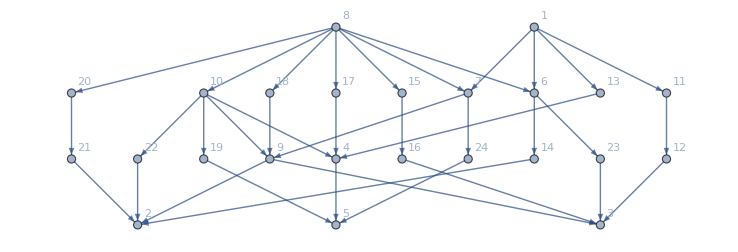

```mathematica
Graph[baseResult["graph with dummies"],DirectedEdges->True,VertexLabels->"Name"]
```

### 1.3.2 Cut Result

```mathematica
dummResCutAmount =Length@Select[Flatten[ cutResult["layers with dummies"]],#≥cutResult["first dummy"]&]
```

9

```mathematica
Sort[Flatten[cutResult["layers with dummies"]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

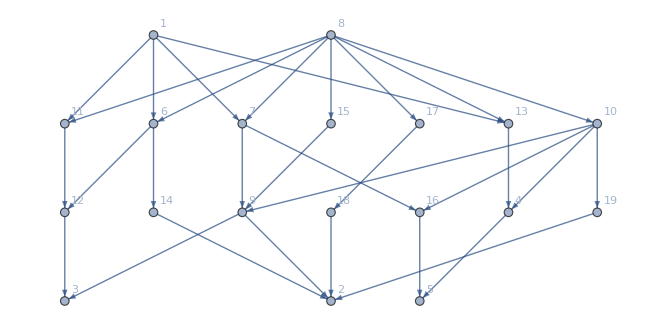

```mathematica
Graph[cutResult["graph with dummies"],DirectedEdges->True,VertexLabels->"Name"]
```

### 1.3.3 Better visualisation

```mathematica
Clear[getNaiveCoords]
getNaiveCoords[layers_]:=MapIndexed[Reverse[#2]{1,-1}&,layers,{2}]
```

```mathematica
coords=getNaiveCoords[cutResult["layers with dummies"]];
```

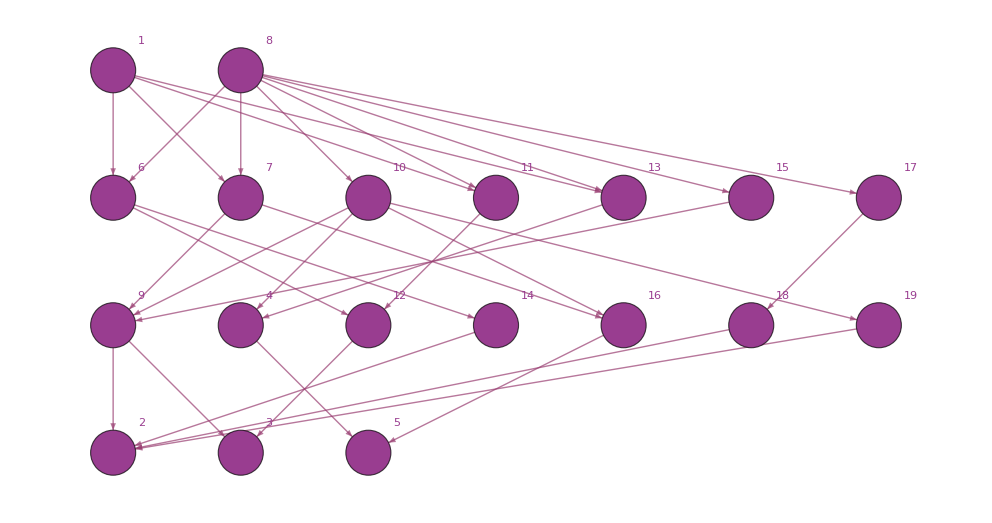

```mathematica
Graph[
Flatten[cutResult["layers with dummies"]],
cutResult["graph with dummies"],VertexShapeFunction->"Circle",VertexSize->{"Scaled",1/Length[Flatten@cutResult["layers with dummies"]]},EdgeStyle->Directive[RGBColor[0.6, 0.24, 0.4428931686004542],Thick],
VertexStyle->RGBColor[0.6, 0.24, 0.5632658430022722],ImageSize->1500,VertexCoordinates->Flatten[coords,1],VertexLabels->"Name"
]
```

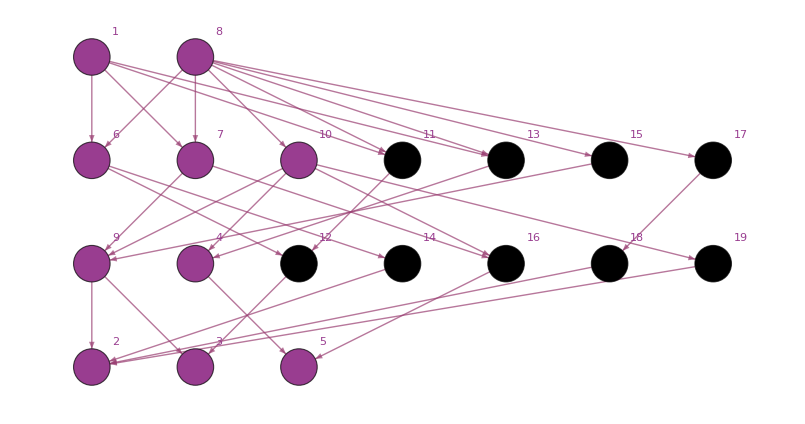

```mathematica
Graph[
Flatten[cutResult["layers with dummies"]],
cutResult["graph with dummies"],VertexShapeFunction->"Circle",VertexSize->{"Scaled",1/Length[Flatten@cutResult["layers with dummies"]]},EdgeStyle->Directive[RGBColor[0.6, 0.24, 0.4428931686004542],Thick],
VertexStyle->{RGBColor[0.6, 0.24, 0.5632658430022722],x_/;x≥cutResult["first dummy"]->Black},ImageSize->1500,VertexCoordinates->Flatten[coords,1],VertexLabels->"Name"
]
```

## 1.4 Test Package AddDummyVertices

```mathematica
AddDummyVertices[Composition[GetLayering,GetDAG][GetGraph[10]],ApproachOption->"Cut"]
```

<|acyclic graph→{1->5,5->2,6->1,6->2,7->9,8->2,8->5,8->7,9->1,9->5,10->1,10->2,10->3},feedback set→{1->8,2->4,2->9,2->10,3->4,4->9,5->6,5->8,5->9,7->8,9->8},graph with dummies→{1->5,5->2,7->9,8->7,9->1,4->3,9->4,6->11,11->12,12->1,6->13,13->14,14->15,15->16,16->2,8->13,8->17,17->18,18->19,19->5,9->20,20->5,10->11,10->13,10->21,21->22,22->23,23->3,8->11,4->16,9->15,6->24,24->25,25->26,26->5,8->27,27->9},layers with dummies→{{8,6,10},{7,11,13,17,21,24,27},{9,12,14,18,22,25},{1,4,15,19,20,23,26},{5,3,16},{2}},first dummy→11|>

```mathematica
AddDummyVertices[Composition[GetLayering,GetDAG][GetGraph[10]],ApproachOption->"Base"]
```

<|acyclic graph→{1->3,1->10,3->5,4->5,6->10,7->1,7->5,8->1,9->6},feedback set→{1->8,2->4,3->7,4->8,5->6,5->8,6->3,6->8,7->8,9->7,10->3,10->6,10->9},graph with dummies→{1->3,6->10,7->1,4->2,8->4,6->5,3->6,8->7,7->9,1->11,11->12,12->10,3->13,13->5,4->14,14->15,15->16,16->5,7->17,17->18,18->19,19->5,8->20,20->1,9->21,21->6,7->22,22->3,8->23,23->24,24->25,25->26,26->5,8->27,27->28,28->29,29->6,3->30,30->10,9->31,31->32,32->10},layers with dummies→{{8},{7,4,20,23,27},{1,2,9,14,17,22,24,28},{3,11,15,18,21,25,29,31},{6,12,13,16,19,26,30,32},{10,5}},first dummy→11|>

```mathematica
AddDummyVertices[Composition[GetLayering,GetDAG][GetGraph[10]],ApproachOption->"Unknown"]
```

AddDummyVertices::option: Option Unknown is not in list of options. Choose another one from the list: 
Base
Cut

$Aborted

## Part II. Улучшающая эвристика

## 2.1 Постановка алгоритма

## 2.2 ImproveHeuristic

### 2.1.1 PromoteVertex

```mathematica
Clear[PromoteVertex,VertexPromotionHeuristic,ImproveHeuristic]
```

```mathematica
PromoteVertex[v_]:=Module[{dummydiff=0,b=relations[v]["parents"]},
s=Table[If[layer[u]==layer[v]+1,
		dummydiff=dummydiff+PromoteVertex[u]],
{u,b}];
layer[v]=layer[v]-1;
dummydiff=dummydiff-Length[relations[v]["parents"]]+Length[relations[v]["children"]];
dummydiff]
```

### 2.1.2 VertexPromotionHeuristic

```mathematica
VertexPromotionHeuristic[]:=Module[{layeringBackUp=layer, promotions=0},
While[promotions==0,
s=Table[
	If[Length[relations[v]["parents"]]>0,
		If[PromoteVertex[v]<0,
			promotions=promotions+1;
			layeringBackUp=layer,
		layer=layeringBackUp]],
{v,V}];
];layer]
```

### 2.1.3 ImproveHeuristic full

```mathematica
ImproveHeuristic[DAG_]:=Module[{g=Graph[Union[DAG["acyclic graph"],Reverse/@DAG["feedback set"]],VertexLabels->"Name"],
V = Flatten[DAG["layers"]],newnames,resultLayer,betterlayers},
relations=Association[Table[v-><|"parents"->Cases[IncidenceList[g,v],e_->h_/;h==v->e],
"children"->Cases[IncidenceList[g,v],e_->h_/;e==v->h]|>,{v,V}]];
newnames=MapIndexed[v[#2⟦1⟧,#1]&,DAG["layers"],{2}];
layer=Association[Thread[Flatten@DAG["layers"]->Flatten[newnames][[All,1]]]];
resultLayer=VertexPromotionHeuristic[];betterlayers=GatherBy[Normal[resultLayer],Last][[All,All,1]];<|"acyclic graph"->DAG["acyclic graph"],"feedback set"->DAG["feedback set"],"layers"->betterlayers|>]
```

### 2.1.4 Test

```mathematica
gr=GetGraph[14];
graphLayering=Composition[GetLayering,GetDAG][gr];
res=ImproveHeuristic[graphLayering]
```

<|acyclic graph→{2->1,2->6,4->1,4->3,4->6,4->12,5->3,5->6,5->12,7->3,7->4,7->5,7->11,7->13,8->1,8->3,8->11,9->5,9->11,9->12,10->3,10->12,11->1,11->4,11->12,11->13,14->1,14->4,14->6,14->10,14->13},feedback set→{1->14,3->1,3->7,3->10,3->11,3->14,4->8,5->7,5->8,5->9,6->10,6->13,8->14,10->4,11->2,12->1,12->2,12->5,12->8,13->9,14->9},layers→{{2,7,9},{14},{8},{5,11},{4,13,1},{10,3},{6,12}}|>

## 2.3 Test From Package (Add Improvment Option)

```mathematica
testGraph=GetGraph[10];
```

```mathematica
dag=GetDAG[testGraph]
```

<|acyclic graph→{1->9,2->3,4->1,4->9,5->2,5->10,6->9,7->6,7->8,10->1},feedback set→{1->5,1->7,1->8,2->5,3->4,3->7,6->4,8->7,9->4,9->5,9->8,10->2}|>

```mathematica
GetLayering[dag]
```

<|acyclic graph→{1->9,2->3,4->1,4->9,5->2,5->10,6->9,7->6,7->8,10->1},feedback set→{1->5,1->7,1->8,2->5,3->4,3->7,6->4,8->7,9->4,9->5,9->8,10->2},layers→{{4,5,7},{2,6,8},{3,10},{1},{9}}|>

```mathematica
GetLayering[dag,ImprovmentOption->True]
```

<|acyclic graph→{1->9,2->3,4->1,4->9,5->2,5->10,6->9,7->6,7->8,10->1},feedback set→{1->5,1->7,1->8,2->5,3->4,3->7,6->4,8->7,9->4,9->5,9->8,10->2},layers→{{4,5,7,6},{2,8,3,10},{1},{9}}|>

```mathematica
GetLayering[dag,ImprovmentOption->False]
```

<|acyclic graph→{1->9,2->3,4->1,4->9,5->2,5->10,6->9,7->6,7->8,10->1},feedback set→{1->5,1->7,1->8,2->5,3->4,3->7,6->4,8->7,9->4,9->5,9->8,10->2},layers→{{4,5,7},{2,6,8},{3,10},{1},{9}}|>

```mathematica
GetLayering[dag,ImprovmentOption->"Unknown"]
```

GetLayering::option: Option Unknown is not in list of options. Choose another one from the list: 
True
False

$Aborted

## Part III. Минимизация ширины слоёв

## 3.1 Min-width(G, W, c) алгоритм

Min Width Heuristic

Input: DAG=(V,A)

assign = {}
fullLayers = {}
num = 1
width = widthUp = 0
while assign ≠ V
	select v ∈ V \ assign with children(v) ⊆ fullLayers and outdegree(v) → max
	if v ≠ null
		put v on layer num
		assign = assign ∪ {v}
		width = width - outdegree(v) + 1
		widthUp += indegree(v)
	if v == null ∨ (width ≥ W ∧ outdegree(v) ==0) ∨ widthUp ≥ c×W
		num++
		fullLayers = fullLayers ∪ assign
		width = widthUp
		widthUp = 0
return layering

## 3.2 Реализация

```mathematica
MinWidthHeuristic[getDagResult_,W_:20,c_:1]:=Module[{dag = Graph[getDagResult["acyclic graph"], VertexLabels->"Name"],
U={},
Z={},
currentLayer=1,
widthCurrent=0,
widthUp=0,
newlayers={},
l,step1,step2},
verticesList=Sort@VertexList[dag];edgesList=EdgeList[dag];adjAssoc=Association@Table[v-><|"parents"-> Select[edgesList,#⟦2⟧==v&]⟦All,1⟧,"children"-> Select[edgesList,#⟦1⟧==v&]⟦All,2⟧|>,{v,verticesList}];
While[
!ContainsExactly[verticesList,U],
step1=Select[Complement[verticesList,U],SubsetQ[Z,adjAssoc[#]["children"]]&];
If[step1!={},
step2=Table[VertexOutDegree[dag, ve],{ve,step1}];
v=step1⟦First[Flatten[Position[step2,Max[step2]]]]⟧,v=0];(*вершина с максимальным количество OutDegree*)
If[
v≠0,
AppendTo[newlayers,{currentLayer,v}];
AppendTo[U,v];
widthCurrent=widthCurrent-VertexOutDegree[dag, v]+1;widthUp=widthUp+VertexInDegree[dag, v]];
If[(v==0)||((widthCurrent≥W )&&(VertexOutDegree[dag, v]==0))||(widthUp≥c*W),
currentLayer++;
Z=Union[Z,U];
widthCurrent=widthUp;
widthUp=0
]
];l=GatherBy[newlayers,First][[All,All,2]];
<|"acyclic graph"->getDagResult["acyclic graph"], "feedback set"->getDagResult["feedback set"],"layers"->l|>]
```

```mathematica
testGraph=GetGraph[12];
```

```mathematica
getdargresult=GetDAG[testGraph];
```

```mathematica
MinWidthHeuristic[getdargresult]
```

<|acyclic graph→{2->1,2->6,2->8,4->1,4->3,4->9,6->3,6->9,6->10,7->1,7->10,10->9,11->5,11->9,12->1,12->3,12->6,12->10},feedback set→{1->11,3->9,3->11,5->2,5->6,5->8,5->11,5->12,6->2,7->2,8->2,9->6,9->7,9->10,9->12,10->6,10->8,11->4},layers→{{1,3,5,8,9},{4,11,10},{6,7},{12,2}}|>

## 3.3 Test Package Option “Min Width”

```mathematica
testGraph=GetGraph[15];
```

```mathematica
getdargresult=GetDAG[testGraph];
```

```mathematica
GetLayering[getdargresult,ApproachOption->{"Min Width",3,1}]
```

<|acyclic graph→{1->9,2->3,2->7,2->13,2->15,3->4,3->5,3->13,4->15,5->1,5->15,6->14,7->1,7->3,7->11,7->15,8->3,8->12,8->13,9->14,10->9,10->13,11->14,11->15,12->9,12->11,12->14,12->15},feedback set→{1->2,1->5,3->12,4->2,4->5,4->9,5->8,5->12,6->12,7->12,9->6,9->12,10->6,10->11,11->8,11->12,13->2,13->3,13->7,14->4,14->8,14->12,14->13,15->5,15->7,15->8},layers→{{13},{14},{6,9},{10,1,15},{5,11},{12,4},{3},{7,8},{2}}|>

```mathematica
GetLayering[getdargresult,ApproachOption->"Min Width"]
```

<|acyclic graph→{1->9,2->3,2->7,2->13,2->15,3->4,3->5,3->13,4->15,5->1,5->15,6->14,7->1,7->3,7->11,7->15,8->3,8->12,8->13,9->14,10->9,10->13,11->14,11->15,12->9,12->11,12->14,12->15},feedback set→{1->2,1->5,3->12,4->2,4->5,4->9,5->8,5->12,6->12,7->12,9->6,9->12,10->6,10->11,11->8,11->12,13->2,13->3,13->7,14->4,14->8,14->12,14->13,15->5,15->7,15->8},layers→{{13,14,15},{11,4,6,9},{12,10,1},{5},{3},{7,8},{2}}|>

```mathematica
GetLayering[getdargresult,ApproachOption->{"Min Width"}]
```

GetLayering::option: Option {Min Width} is not in list of options. Choose another one from the list: 
Longest Path
Exact
Min Width

$Aborted